```mathematica
In[106]:= Sum[(p^-l (1-1/p))/(ω^2+p^(-2z(l))),{l,-∞,∞}]

In[105]:= Sum[2^l/(4+4^l),{l,0,∞}]//FullSimplify

Out[105]= ∑_(l = 0)^∞ 

Integrate[(p^(-l+m) (1-1/p))/(ω^2+p^(-2z(l-m))),{l,0,∞}]

Out[20]= ∫_0^∞ 

In[104]:= (p^(-l+m) (1-1/p))/(ω^2+p^(-2z(l-m)))/.{m->1,z->1,ω->1,p->2}//FullSimplify

Out[104]= 2^l/(4+4^l)

In[110]:= Integrate[E^(-2π I ω τ)/(ω^2+1),{ω,-∞,∞}]

Out[110]= ConditionalExpression[E^(-2 π Abs[τ]) π,τ∈ℝ]

In[129]:= Sum[E^(-2 π p^(-z l) Abs[τ]) π p^(l z-l) (1-1/p)/.{p->2,z->0.5,τ->1},{l,-100,100}]

正在计算In[129]:= General::munfl: Exp[-7.07424*10^15] is too small to represent as a normalized machine number; precision may be lost.

正在计算In[129]:= General::munfl: Exp[-5.00224*10^15] is too small to represent as a normalized machine number; precision may be lost.

正在计算In[129]:= General::munfl: Exp[-3.53712*10^15] is too small to represent as a normalized machine number; precision may be lost.

正在计算In[129]:= General::stop: Further output of General::munfl will be suppressed during this calculation.

Out[129]= 0.721348

In[122]:= Sum[E^(-2 π p^(-z l) Abs[τ]) π p^(l z-l) (1-1/p)/.{p->2,z->0.5,τ->1},{l,0,100}]

Out[122]= 0.721029

In[225]:= listt=Table[((-E^(-2π Abs[E^τ]p^z)/p^z/.{p->31,z->1/2})+Sum[E^(-2 π p^(-z l) Abs[E^τ])  p^(l z-l) (1-1/p)/.{p->31,z->1/2},{l,0,100}])/Abs[E^τ]^(-1/z+1)/.{p->31,z->1/2},{τ,2,10,0.01}];

正在计算In[225]:= General::munfl: Exp[-709.72] is too small to represent as a normalized machine number; precision may be lost.

正在计算In[225]:= General::munfl: Exp[-716.853] is too small to represent as a normalized machine number; precision may be lost.

正在计算In[225]:= General::munfl: Exp[-724.057] is too small to represent as a normalized machine number; precision may be lost.

正在计算In[225]:= General::stop: Further output of General::munfl will be suppressed during this calculation.

In[226]:= ListPlot[listt,PlotRange->All]

Out[226]= 

In[201]:= N[listt[[1]]-listt[[2]]]

正在计算In[201]:= General::munfl: Exp[-888.665] is too small to represent as a normalized machine number; precision may be lost.

正在计算In[201]:= General::munfl: Exp[-888.577] is too small to represent as a normalized machine number; precision may be lost.

Out[201]= -2.22045*10^-16

In[209]:= E^(-π^2/(0.5Log[31]))

Out[209]= 0.00318855

In[216]:= 0.5Log[31]

Out[216]= 1.71699

In[133]:= listt0=Table[Sum[E^(-2 π p^(-z l) Abs[τ]) π p^(l z-l) (1-1/p)/.{p->2,z->0.5,τ->1},{l,-100,100}],{τ,1,1000,1}];

正在计算In[133]:= General::munfl: Exp[-7.07424*10^15] is too small to represent as a normalized machine number; precision may be lost.

正在计算In[133]:= General::munfl: Exp[-5.00224*10^15] is too small to represent as a normalized machine number; precision may be lost.

正在计算In[133]:= General::munfl: Exp[-3.53712*10^15] is too small to represent as a normalized machine number; precision may be lost.

正在计算In[133]:= General::stop: Further output of General::munfl will be suppressed during this calculation.

In[134]:= ListPlot[listt0]

Out[134]= 

In[233]:= Integrate[E^(-2π I v u) p^(v(z-1)) E^-p^(-v z),{v,-∞,∞}]

Out[233]= ∫_(-∞)^∞ 

In[232]:= Clear[v]
```

SetDelayed::write: Tag In in In[106] is Protected.

$Failed

Syntax::sntxf: "" cannot be followed by "l))),{l,-∞,∞}]".

Syntax::sntxf: "" cannot be followed by 
    "In[106]:= Sum[(p^-l (1-1/p))/(ω^2+p^(-2z(l))),{l,-∞,∞}]".

```mathematica
listt=Table[((-E^(-2π Abs[E^τ]p^z)/p^z/.{p->31,z->1/2})+Sum[E^(-2 π p^(-z l) Abs[E^τ])  p^(l z-l) (1-1/p)/.{p->31,z->1/2},{l,0,100}])/Abs[E^τ]^(-1/z+1)/.{p->31,z->1/2},{τ,2,10,0.01}];
```

General::munfl: Exp[-709.72] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-716.853] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-724.057] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

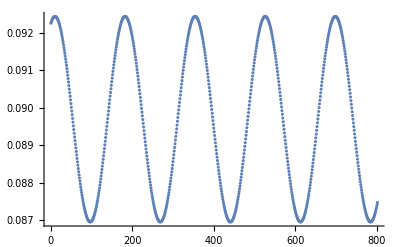

```mathematica
ListPlot[listt,PlotRange->All]
```